```mathematica
SetDirectory[NotebookDirectory[]];
rawData = Import["Segmented 2/3.json"];
```

```mathematica
Head[rawData]
```

List

```mathematica
coords = {};
"shapes"/. rawData;
AppendTo[coords, "points"/. #]&/@%;
```

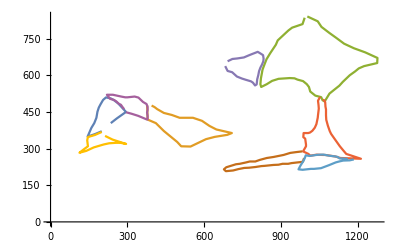

```mathematica
ListLinePlot[coords]
```